```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/big_brother/Documents/TaskDash/Boundary/separation

```mathematica
fo = Import["exp_fo.txt","Table"][[12;;]];
xh = Import["exp_xh.txt","Table"][[12;;]];
```

```mathematica
fo = ({fo[[1]],fo[[#]]})ᵀ&/@Range[2,4];
xh =({xh[[1]],xh[[#]] })ᵀ&/@Range[2,4];
```

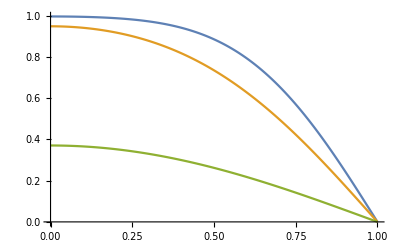

```mathematica
ListPlot[fo, Joined->True]
```

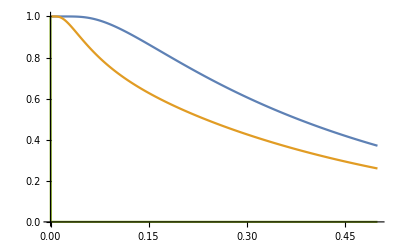

```mathematica
ListPlot[xh, Joined->True]
```

```mathematica
xh[[3]]
```

{{0.,1.},{0.000500501,0.00033994},{0.001001,0.000240558},{0.0015015,0.00019653},{0.002002,0.000170285},{0.0025025,0.000152374},{0.003003,0.000139154},{0.0035035,0.00012888},{0.004004,0.000120599},{0.0045045,0.00011374},{0.00500501,0.000107938},{0.00550551,0.000102947},{0.00600601,0.0000985934},{0.00650651,0.0000947527},{0.00700701,0.0000913313},{0.00750751,0.0000882582},{0.00800801,0.0000854779},{0.00850851,0.0000829468},{0.00900901,0.0000806298},{0.00950951,0.0000784981},{0.01001,0.0000765285},{0.0105105,0.0000747012},{0.011011,0.000073},{0.0115115,0.000071411},{0.012012,0.0000699223},{0.0125125,0.0000685239},{0.013013,0.0000672069},{0.0135135,0.0000659637},{0.014014,0.0000647877},{0.0145145,0.000063673},{0.015015,0.0000626145},{0.0155155,0.0000616076},{0.016016,0.0000606482},{0.0165165,0.0000597328},{0.017017,0.0000588579},{0.0175175,0.0000580208},{0.018018,0.0000572188},{0.0185185,0.0000564495},{0.019019,0.0000557107},{0.0195195,0.0000550005},{0.02002,0.000054317},{0.0205205,0.0000536586},{0.021021,0.0000530238},{0.0215215,0.0000524113},{0.022022,0.0000518197},{0.0225225,0.000051248},{0.023023,0.0000506949},{0.0235235,0.0000501595},{0.024024,0.0000496409},{0.0245245,0.0000491383},{0.025025,0.0000486507},{0.0255255,0.0000481775},{0.026026,0.000047718},{0.0265265,0.0000472715},{0.027027,0.0000468375},{0.0275275,0.0000464153},{0.028028,0.0000460044},{0.0285285,0.0000456044},{0.029029,0.0000452147},{0.0295295,0.0000448349},{0.03003,0.0000444647},{0.0305305,0.0000441035},{0.031031,0.0000437511},{0.0315315,0.0000434071},{0.032032,0.0000430711},{0.0325325,0.0000427429},{0.033033,0.0000424222},{0.0335335,0.0000421086},{0.034034,0.000041802},{0.0345345,0.000041502},{0.035035,0.0000412085},{0.0355355,0.0000409211},{0.036036,0.0000406398},{0.0365365,0.0000403642},{0.037037,0.0000400942},{0.0375375,0.0000398295},{0.038038,0.0000395702},{0.0385385,0.0000393158},{0.039039,0.0000390663},{0.0395395,0.0000388216},{0.04004,0.0000385815},{0.0405405,0.0000383458},{0.041041,0.0000381144},{0.0415415,0.0000378871},{0.042042,0.000037664},{0.0425425,0.0000374447},{0.043043,0.0000372293},{0.0435435,0.0000370176},{0.044044,0.0000368095},{0.0445445,0.0000366049},{0.045045,0.0000364036},{0.0455455,0.0000362057},{0.046046,0.0000360111},{0.0465465,0.0000358195},{0.047047,0.000035631},{0.0475475,0.0000354455},{0.048048,0.0000352628},{0.0485485,0.000035083},{0.049049,0.0000349059},{0.0495495,0.0000347315},{0.0500501,0.0000345598},{0.0505506,0.0000343905},{0.0510511,0.0000342237},{0.0515516,0.0000340594},{0.0520521,0.0000338974},{0.0525526,0.0000337377},{0.0530531,0.0000335803},{0.0535536,0.0000334251},{0.0540541,0.000033272},{0.0545546,0.000033121},{0.0550551,0.0000329721},{0.0555556,0.0000328252},{0.0560561,0.0000326803},{0.0565566,0.0000325372},{0.0570571,0.0000323961},{0.0575576,0.0000322567},{0.0580581,0.0000321192},{0.0585586,0.0000319834},{0.0590591,0.0000318494},{0.0595596,0.000031717},{0.0600601,0.0000315863},{0.0605606,0.0000314572},{0.0610611,0.0000313296},{0.0615616,0.0000312037},{0.0620621,0.0000310792},{0.0625626,0.0000309562},{0.0630631,0.0000308347},{0.0635636,0.0000307146},{0.0640641,0.0000305959},{0.0645646,0.0000304786},{0.0650651,0.0000303626},{0.0655656,0.000030248},{0.0660661,0.0000301346},{0.0665666,0.0000300226},{0.0670671,0.0000299117},{0.0675676,0.0000298021},{0.0680681,0.0000296937},{0.0685686,0.0000295865},{0.0690691,0.0000294805},{0.0695696,0.0000293756},{0.0700701,0.0000292718},{0.0705706,0.0000291691},{0.0710711,0.0000290674},{0.0715716,0.0000289669},{0.0720721,0.0000288673},{0.0725726,0.0000287688},{0.0730731,0.0000286714},{0.0735736,0.0000285749},{0.0740741,0.0000284793},{0.0745746,0.0000283848},{0.0750751,0.0000282911},{0.0755756,0.0000281984},{0.0760761,0.0000281066},{0.0765766,0.0000280157},{0.0770771,0.0000279257},{0.0775776,0.0000278365},{0.0780781,0.0000277482},{0.0785786,0.0000276608},{0.0790791,0.0000275741},{0.0795796,0.0000274883},{0.0800801,0.0000274032},{0.0805806,0.000027319},{0.0810811,0.0000272355},{0.0815816,0.0000271528},{0.0820821,0.0000270708},{0.0825826,0.0000269896},{0.0830831,0.0000269091},{0.0835836,0.0000268294},{0.0840841,0.0000267503},{0.0845846,0.0000266719},{0.0850851,0.0000265942},{0.0855856,0.0000265172},{0.0860861,0.0000264409},{0.0865866,0.0000263652},{0.0870871,0.0000262901},{0.0875876,0.0000262157},{0.0880881,0.0000261419},{0.0885886,0.0000260688},{0.0890891,0.0000259962},{0.0895896,0.0000259243},{0.0900901,0.0000258529},{0.0905906,0.0000257822},{0.0910911,0.000025712},{0.0915916,0.0000256423},{0.0920921,0.0000255733},{0.0925926,0.0000255048},{0.0930931,0.0000254368},{0.0935936,0.0000253694},{0.0940941,0.0000253025},{0.0945946,0.0000252361},{0.0950951,0.0000251703},{0.0955956,0.0000251049},{0.0960961,0.0000250401},{0.0965966,0.0000249757},{0.0970971,0.0000249119},{0.0975976,0.0000248485},{0.0980981,0.0000247856},{0.0985986,0.0000247232},{0.0990991,0.0000246612},{0.0995996,0.0000245997},{0.1001,0.0000245387},{0.100601,0.0000244781},{0.101101,0.0000244179},{0.101602,0.0000243582},{0.102102,0.0000242989},{0.102603,0.00002424},{0.103103,0.0000241816},{0.103604,0.0000241236},{0.104104,0.000024066},{0.104605,0.0000240087},{0.105105,0.0000239519},{0.105606,0.0000238955},{0.106106,0.0000238395},{0.106607,0.0000237838},{0.107107,0.0000237286},{0.107608,0.0000236737},{0.108108,0.0000236192},{0.108609,0.000023565},{0.109109,0.0000235112},{0.10961,0.0000234578},{0.11011,0.0000234047},{0.110611,0.000023352},{0.111111,0.0000232996},{0.111612,0.0000232476},{0.112112,0.0000231959},{0.112613,0.0000231445},{0.113113,0.0000230935},{0.113614,0.0000230427},{0.114114,0.0000229924},{0.114615,0.0000229423},{0.115115,0.0000228925},{0.115616,0.0000228431},{0.116116,0.0000227939},{0.116617,0.0000227451},{0.117117,0.0000226966},{0.117618,0.0000226483},{0.118118,0.0000226004},{0.118619,0.0000225528},{0.119119,0.0000225054},{0.11962,0.0000224583},{0.12012,0.0000224115},{0.120621,0.000022365},{0.121121,0.0000223188},{0.121622,0.0000222728},{0.122122,0.0000222271},{0.122623,0.0000221817},{0.123123,0.0000221365},{0.123624,0.0000220916},{0.124124,0.0000220469},{0.124625,0.0000220025},{0.125125,0.0000219584},{0.125626,0.0000219145},{0.126126,0.0000218708},{0.126627,0.0000218274},{0.127127,0.0000217842},{0.127628,0.0000217413},{0.128128,0.0000216986},{0.128629,0.0000216562},{0.129129,0.0000216139},{0.12963,0.0000215719},{0.13013,0.0000215302},{0.130631,0.0000214886},{0.131131,0.0000214473},{0.131632,0.0000214062},{0.132132,0.0000213653},{0.132633,0.0000213246},{0.133133,0.0000212842},{0.133634,0.0000212439},{0.134134,0.0000212039},{0.134635,0.000021164},{0.135135,0.0000211244},{0.135636,0.000021085},{0.136136,0.0000210457},{0.136637,0.0000210067},{0.137137,0.0000209679},{0.137638,0.0000209292},{0.138138,0.0000208908},{0.138639,0.0000208525},{0.139139,0.0000208145},{0.13964,0.0000207766},{0.14014,0.0000207389},{0.140641,0.0000207013},{0.141141,0.000020664},{0.141642,0.0000206269},{0.142142,0.0000205899},{0.142643,0.0000205531},{0.143143,0.0000205164},{0.143644,0.00002048},{0.144144,0.0000204437},{0.144645,0.0000204076},{0.145145,0.0000203716},{0.145646,0.0000203358},{0.146146,0.0000203002},{0.146647,0.0000202647},{0.147147,0.0000202294},{0.147648,0.0000201943},{0.148148,0.0000201593},{0.148649,0.0000201245},{0.149149,0.0000200898},{0.14965,0.0000200553},{0.15015,0.0000200209},{0.150651,0.0000199867},{0.151151,0.0000199526},{0.151652,0.0000199187},{0.152152,0.0000198849},{0.152653,0.0000198513},{0.153153,0.0000198178},{0.153654,0.0000197844},{0.154154,0.0000197512},{0.154655,0.0000197182},{0.155155,0.0000196852},{0.155656,0.0000196524},{0.156156,0.0000196198},{0.156657,0.0000195873},{0.157157,0.0000195549},{0.157658,0.0000195226},{0.158158,0.0000194905},{0.158659,0.0000194585},{0.159159,0.0000194266},{0.15966,0.0000193949},{0.16016,0.0000193632},{0.160661,0.0000193318},{0.161161,0.0000193004},{0.161662,0.0000192691},{0.162162,0.000019238},{0.162663,0.000019207},{0.163163,0.0000191761},{0.163664,0.0000191454},{0.164164,0.0000191147},{0.164665,0.0000190842},{0.165165,0.0000190537},{0.165666,0.0000190234},{0.166166,0.0000189932},{0.166667,0.0000189632},{0.167167,0.0000189332},{0.167668,0.0000189033},{0.168168,0.0000188736},{0.168669,0.0000188439},{0.169169,0.0000188144},{0.16967,0.000018785},{0.17017,0.0000187557},{0.170671,0.0000187264},{0.171171,0.0000186973},{0.171672,0.0000186683},{0.172172,0.0000186394},{0.172673,0.0000186106},{0.173173,0.0000185819},{0.173674,0.0000185533},{0.174174,0.0000185248},{0.174675,0.0000184963},{0.175175,0.000018468},{0.175676,0.0000184398},{0.176176,0.0000184117},{0.176677,0.0000183836},{0.177177,0.0000183557},{0.177678,0.0000183279},{0.178178,0.0000183001},{0.178679,0.0000182724},{0.179179,0.0000182449},{0.17968,0.0000182174},{0.18018,0.00001819},{0.180681,0.0000181627},{0.181181,0.0000181355},{0.181682,0.0000181083},{0.182182,0.0000180813},{0.182683,0.0000180543},{0.183183,0.0000180275},{0.183684,0.0000180007},{0.184184,0.000017974},{0.184685,0.0000179473},{0.185185,0.0000179208},{0.185686,0.0000178943},{0.186186,0.000017868},{0.186687,0.0000178417},{0.187187,0.0000178154},{0.187688,0.0000177893},{0.188188,0.0000177632},{0.188689,0.0000177373},{0.189189,0.0000177114},{0.18969,0.0000176855},{0.19019,0.0000176598},{0.190691,0.0000176341},{0.191191,0.0000176085},{0.191692,0.000017583},{0.192192,0.0000175575},{0.192693,0.0000175321},{0.193193,0.0000175068},{0.193694,0.0000174816},{0.194194,0.0000174564},{0.194695,0.0000174313},{0.195195,0.0000174063},{0.195696,0.0000173813},{0.196196,0.0000173564},{0.196697,0.0000173316},{0.197197,0.0000173069},{0.197698,0.0000172822},{0.198198,0.0000172576},{0.198699,0.000017233},{0.199199,0.0000172085},{0.1997,0.0000171841},{0.2002,0.0000171598},{0.200701,0.0000171355},{0.201201,0.0000171112},{0.201702,0.0000170871},{0.202202,0.000017063},{0.202703,0.000017039},{0.203203,0.000017015},{0.203704,0.0000169911},{0.204204,0.0000169672},{0.204705,0.0000169435},{0.205205,0.0000169197},{0.205706,0.0000168961},{0.206206,0.0000168725},{0.206707,0.0000168489},{0.207207,0.0000168254},{0.207708,0.000016802},{0.208208,0.0000167786},{0.208709,0.0000167553},{0.209209,0.0000167321},{0.20971,0.0000167089},{0.21021,0.0000166858},{0.210711,0.0000166627},{0.211211,0.0000166396},{0.211712,0.0000166167},{0.212212,0.0000165938},{0.212713,0.0000165709},{0.213213,0.0000165481},{0.213714,0.0000165254},{0.214214,0.0000165027},{0.214715,0.00001648},{0.215215,0.0000164574},{0.215716,0.0000164349},{0.216216,0.0000164124},{0.216717,0.00001639},{0.217217,0.0000163676},{0.217718,0.0000163453},{0.218218,0.000016323},{0.218719,0.0000163008},{0.219219,0.0000162786},{0.21972,0.0000162564},{0.22022,0.0000162344},{0.220721,0.0000162123},{0.221221,0.0000161904},{0.221722,0.0000161684},{0.222222,0.0000161466},{0.222723,0.0000161247},{0.223223,0.0000161029},{0.223724,0.0000160812},{0.224224,0.0000160595},{0.224725,0.0000160379},{0.225225,0.0000160163},{0.225726,0.0000159947},{0.226226,0.0000159732},{0.226727,0.0000159518},{0.227227,0.0000159304},{0.227728,0.000015909},{0.228228,0.0000158877},{0.228729,0.0000158664},{0.229229,0.0000158452},{0.22973,0.000015824},{0.23023,0.0000158028},{0.230731,0.0000157817},{0.231231,0.0000157607},{0.231732,0.0000157397},{0.232232,0.0000157187},{0.232733,0.0000156978},{0.233233,0.0000156769},{0.233734,0.0000156561},{0.234234,0.0000156353},{0.234735,0.0000156145},{0.235235,0.0000155938},{0.235736,0.0000155731},{0.236236,0.0000155525},{0.236737,0.0000155319},{0.237237,0.0000155114},{0.237738,0.0000154909},{0.238238,0.0000154704},{0.238739,0.00001545},{0.239239,0.0000154296},{0.23974,0.0000154092},{0.24024,0.0000153889},{0.240741,0.0000153686},{0.241241,0.0000153484},{0.241742,0.0000153282},{0.242242,0.0000153081},{0.242743,0.000015288},{0.243243,0.0000152679},{0.243744,0.0000152478},{0.244244,0.0000152278},{0.244745,0.0000152079},{0.245245,0.000015188},{0.245746,0.0000151681},{0.246246,0.0000151482},{0.246747,0.0000151284},{0.247247,0.0000151086},{0.247748,0.0000150889},{0.248248,0.0000150692},{0.248749,0.0000150495},{0.249249,0.0000150299},{0.24975,0.0000150103},{0.25025,0.0000149907},{0.250751,0.0000149712},{0.251251,0.0000149517},{0.251752,0.0000149323},{0.252252,0.0000149129},{0.252753,0.0000148935},{0.253253,0.0000148741},{0.253754,0.0000148548},{0.254254,0.0000148355},{0.254755,0.0000148163},{0.255255,0.0000147971},{0.255756,0.0000147779},{0.256256,0.0000147588},{0.256757,0.0000147397},{0.257257,0.0000147206},{0.257758,0.0000147015},{0.258258,0.0000146825},{0.258759,0.0000146636},{0.259259,0.0000146446},{0.25976,0.0000146257},{0.26026,0.0000146068},{0.260761,0.000014588},{0.261261,0.0000145692},{0.261762,0.0000145504},{0.262262,0.0000145316},{0.262763,0.0000145129},{0.263263,0.0000144942},{0.263764,0.0000144756},{0.264264,0.000014457},{0.264765,0.0000144384},{0.265265,0.0000144198},{0.265766,0.0000144013},{0.266266,0.0000143828},{0.266767,0.0000143643},{0.267267,0.0000143459},{0.267768,0.0000143275},{0.268268,0.0000143091},{0.268769,0.0000142908},{0.269269,0.0000142724},{0.26977,0.0000142542},{0.27027,0.0000142359},{0.270771,0.0000142177},{0.271271,0.0000141995},{0.271772,0.0000141813},{0.272272,0.0000141632},{0.272773,0.0000141451},{0.273273,0.000014127},{0.273774,0.000014109},{0.274274,0.0000140909},{0.274775,0.0000140729},{0.275275,0.000014055},{0.275776,0.0000140371},{0.276276,0.0000140192},{0.276777,0.0000140013},{0.277277,0.0000139834},{0.277778,0.0000139656},{0.278278,0.0000139478},{0.278779,0.0000139301},{0.279279,0.0000139123},{0.27978,0.0000138946},{0.28028,0.0000138769},{0.280781,0.0000138593},{0.281281,0.0000138417},{0.281782,0.0000138241},{0.282282,0.0000138065},{0.282783,0.000013789},{0.283283,0.0000137714},{0.283784,0.000013754},{0.284284,0.0000137365},{0.284785,0.0000137191},{0.285285,0.0000137017},{0.285786,0.0000136843},{0.286286,0.0000136669},{0.286787,0.0000136496},{0.287287,0.0000136323},{0.287788,0.000013615},{0.288288,0.0000135978},{0.288789,0.0000135806},{0.289289,0.0000135634},{0.28979,0.0000135462},{0.29029,0.0000135291},{0.290791,0.0000135119},{0.291291,0.0000134949},{0.291792,0.0000134778},{0.292292,0.0000134607},{0.292793,0.0000134437},{0.293293,0.0000134267},{0.293794,0.0000134098},{0.294294,0.0000133928},{0.294795,0.0000133759},{0.295295,0.000013359},{0.295796,0.0000133422},{0.296296,0.0000133253},{0.296797,0.0000133085},{0.297297,0.0000132917},{0.297798,0.000013275},{0.298298,0.0000132582},{0.298799,0.0000132415},{0.299299,0.0000132248},{0.2998,0.0000132082},{0.3003,0.0000131915},{0.300801,0.0000131749},{0.301301,0.0000131583},{0.301802,0.0000131417},{0.302302,0.0000131252},{0.302803,0.0000131087},{0.303303,0.0000130922},{0.303804,0.0000130757},{0.304304,0.0000130593},{0.304805,0.0000130428},{0.305305,0.0000130264},{0.305806,0.0000130101},{0.306306,0.0000129937},{0.306807,0.0000129774},{0.307307,0.0000129611},{0.307808,0.0000129448},{0.308308,0.0000129285},{0.308809,0.0000129123},{0.309309,0.0000128961},{0.30981,0.0000128799},{0.31031,0.0000128637},{0.310811,0.0000128476},{0.311311,0.0000128315},{0.311812,0.0000128154},{0.312312,0.0000127993},{0.312813,0.0000127832},{0.313313,0.0000127672},{0.313814,0.0000127512},{0.314314,0.0000127352},{0.314815,0.0000127192},{0.315315,0.0000127033},{0.315816,0.0000126874},{0.316316,0.0000126715},{0.316817,0.0000126556},{0.317317,0.0000126398},{0.317818,0.0000126239},{0.318318,0.0000126081},{0.318819,0.0000125923},{0.319319,0.0000125766},{0.31982,0.0000125608},{0.32032,0.0000125451},{0.320821,0.0000125294},{0.321321,0.0000125137},{0.321822,0.0000124981},{0.322322,0.0000124824},{0.322823,0.0000124668},{0.323323,0.0000124512},{0.323824,0.0000124357},{0.324324,0.0000124201},{0.324825,0.0000124046},{0.325325,0.0000123891},{0.325826,0.0000123736},{0.326326,0.0000123582},{0.326827,0.0000123427},{0.327327,0.0000123273},{0.327828,0.0000123119},{0.328328,0.0000122965},{0.328829,0.0000122812},{0.329329,0.0000122658},{0.32983,0.0000122505},{0.33033,0.0000122352},{0.330831,0.0000122199},{0.331331,0.0000122047},{0.331832,0.0000121895},{0.332332,0.0000121743},{0.332833,0.0000121591},{0.333333,0.0000121439},{0.333834,0.0000121287},{0.334334,0.0000121136},{0.334835,0.0000120985},{0.335335,0.0000120834},{0.335836,0.0000120684},{0.336336,0.0000120533},{0.336837,0.0000120383},{0.337337,0.0000120233},{0.337838,0.0000120083},{0.338338,0.0000119933},{0.338839,0.0000119784},{0.339339,0.0000119635},{0.33984,0.0000119485},{0.34034,0.0000119337},{0.340841,0.0000119188},{0.341341,0.0000119039},{0.341842,0.0000118891},{0.342342,0.0000118743},{0.342843,0.0000118595},{0.343343,0.0000118448},{0.343844,0.00001183},{0.344344,0.0000118153},{0.344845,0.0000118006},{0.345345,0.0000117859},{0.345846,0.0000117712},{0.346346,0.0000117566},{0.346847,0.0000117419},{0.347347,0.0000117273},{0.347848,0.0000117127},{0.348348,0.0000116982},{0.348849,0.0000116836},{0.349349,0.0000116691},{0.34985,0.0000116546},{0.35035,0.0000116401},{0.350851,0.0000116256},{0.351351,0.0000116111},{0.351852,0.0000115967},{0.352352,0.0000115823},{0.352853,0.0000115679},{0.353353,0.0000115535},{0.353854,0.0000115391},{0.354354,0.0000115248},{0.354855,0.0000115105},{0.355355,0.0000114962},{0.355856,0.0000114819},{0.356356,0.0000114676},{0.356857,0.0000114534},{0.357357,0.0000114391},{0.357858,0.0000114249},{0.358358,0.0000114107},{0.358859,0.0000113965},{0.359359,0.0000113824},{0.35986,0.0000113683},{0.36036,0.0000113541},{0.360861,0.00001134},{0.361361,0.0000113259},{0.361862,0.0000113119},{0.362362,0.0000112978},{0.362863,0.0000112838},{0.363363,0.0000112698},{0.363864,0.0000112558},{0.364364,0.0000112418},{0.364865,0.0000112279},{0.365365,0.0000112139},{0.365866,0.0000112},{0.366366,0.0000111861},{0.366867,0.0000111722},{0.367367,0.0000111584},{0.367868,0.0000111445},{0.368368,0.0000111307},{0.368869,0.0000111169},{0.369369,0.0000111031},{0.36987,0.0000110893},{0.37037,0.0000110756},{0.370871,0.0000110618},{0.371371,0.0000110481},{0.371872,0.0000110344},{0.372372,0.0000110207},{0.372873,0.000011007},{0.373373,0.0000109934},{0.373874,0.0000109798},{0.374374,0.0000109661},{0.374875,0.0000109525},{0.375375,0.000010939},{0.375876,0.0000109254},{0.376376,0.0000109118},{0.376877,0.0000108983},{0.377377,0.0000108848},{0.377878,0.0000108713},{0.378378,0.0000108578},{0.378879,0.0000108444},{0.379379,0.0000108309},{0.37988,0.0000108175},{0.38038,0.0000108041},{0.380881,0.0000107907},{0.381381,0.0000107773},{0.381882,0.000010764},{0.382382,0.0000107506},{0.382883,0.0000107373},{0.383383,0.000010724},{0.383884,0.0000107107},{0.384384,0.0000106975},{0.384885,0.0000106842},{0.385385,0.000010671},{0.385886,0.0000106577},{0.386386,0.0000106445},{0.386887,0.0000106314},{0.387387,0.0000106182},{0.387888,0.000010605},{0.388388,0.0000105919},{0.388889,0.0000105788},{0.389389,0.0000105657},{0.38989,0.0000105526},{0.39039,0.0000105395},{0.390891,0.0000105265},{0.391391,0.0000105134},{0.391892,0.0000105004},{0.392392,0.0000104874},{0.392893,0.0000104744},{0.393393,0.0000104615},{0.393894,0.0000104485},{0.394394,0.0000104356},{0.394895,0.0000104226},{0.395395,0.0000104097},{0.395896,0.0000103968},{0.396396,0.000010384},{0.396897,0.0000103711},{0.397397,0.0000103583},{0.397898,0.0000103455},{0.398398,0.0000103327},{0.398899,0.0000103199},{0.399399,0.0000103071},{0.3999,0.0000102943},{0.4004,0.0000102816},{0.400901,0.0000102689},{0.401401,0.0000102562},{0.401902,0.0000102435},{0.402402,0.0000102308},{0.402903,0.0000102181},{0.403403,0.0000102055},{0.403904,0.0000101929},{0.404404,0.0000101802},{0.404905,0.0000101676},{0.405405,0.0000101551},{0.405906,0.0000101425},{0.406406,0.0000101299},{0.406907,0.0000101174},{0.407407,0.0000101049},{0.407908,0.0000100924},{0.408408,0.0000100799},{0.408909,0.0000100674},{0.409409,0.000010055},{0.40991,0.0000100425},{0.41041,0.0000100301},{0.410911,0.0000100177},{0.411411,0.0000100053},{0.411912,9.99294×10^-6},{0.412412,9.98058×10^-6},{0.412913,9.96824×10^-6},{0.413413,9.95591×10^-6},{0.413914,9.94359×10^-6},{0.414414,9.93129×10^-6},{0.414915,9.91901×10^-6},{0.415415,9.90674×10^-6},{0.415916,9.89449×10^-6},{0.416416,9.88225×10^-6},{0.416917,9.87003×10^-6},{0.417417,9.85782×10^-6},{0.417918,9.84563×10^-6},{0.418418,9.83346×10^-6},{0.418919,9.8213×10^-6},{0.419419,9.80915×10^-6},{0.41992,9.79702×10^-6},{0.42042,9.78491×10^-6},{0.420921,9.77281×10^-6},{0.421421,9.76072×10^-6},{0.421922,9.74866×10^-6},{0.422422,9.7366×10^-6},{0.422923,9.72456×10^-6},{0.423423,9.71254×10^-6},{0.423924,9.70053×10^-6},{0.424424,9.68854×10^-6},{0.424925,9.67656×10^-6},{0.425425,9.6646×10^-6},{0.425926,9.65265×10^-6},{0.426426,9.64071×10^-6},{0.426927,9.6288×10^-6},{0.427427,9.61689×10^-6},{0.427928,9.605×10^-6},{0.428428,9.59313×10^-6},{0.428929,9.58127×10^-6},{0.429429,9.56943×10^-6},{0.42993,9.5576×10^-6},{0.43043,9.54578×10^-6},{0.430931,9.53398×10^-6},{0.431431,9.5222×10^-6},{0.431932,9.51043×10^-6},{0.432432,9.49867×10^-6},{0.432933,9.48693×10^-6},{0.433433,9.47521×10^-6},{0.433934,9.4635×10^-6},{0.434434,9.4518×10^-6},{0.434935,9.44012×10^-6},{0.435435,9.42845×10^-6},{0.435936,9.4168×10^-6},{0.436436,9.40516×10^-6},{0.436937,9.39354×10^-6},{0.437437,9.38193×10^-6},{0.437938,9.37033×10^-6},{0.438438,9.35875×10^-6},{0.438939,9.34719×10^-6},{0.439439,9.33564×10^-6},{0.43994,9.3241×10^-6},{0.44044,9.31258×10^-6},{0.440941,9.30107×10^-6},{0.441441,9.28957×10^-6},{0.441942,9.2781×10^-6},{0.442442,9.26663×10^-6},{0.442943,9.25518×10^-6},{0.443443,9.24374×10^-6},{0.443944,9.23232×10^-6},{0.444444,9.22091×10^-6},{0.444945,9.20952×10^-6},{0.445445,9.19814×10^-6},{0.445946,9.18678×10^-6},{0.446446,9.17542×10^-6},{0.446947,9.16409×10^-6},{0.447447,9.15276×10^-6},{0.447948,9.14146×10^-6},{0.448448,9.13016×10^-6},{0.448949,9.11888×10^-6},{0.449449,9.10762×10^-6},{0.44995,9.09636×10^-6},{0.45045,9.08512×10^-6},{0.450951,9.0739×10^-6},{0.451451,9.06269×10^-6},{0.451952,9.05149×10^-6},{0.452452,9.04031×10^-6},{0.452953,9.02914×10^-6},{0.453453,9.01799×10^-6},{0.453954,9.00685×10^-6},{0.454454,8.99572×10^-6},{0.454955,8.98461×10^-6},{0.455455,8.97351×10^-6},{0.455956,8.96242×10^-6},{0.456456,8.95135×10^-6},{0.456957,8.94029×10^-6},{0.457457,8.92925×10^-6},{0.457958,8.91822×10^-6},{0.458458,8.9072×10^-6},{0.458959,8.8962×10^-6},{0.459459,8.88521×10^-6},{0.45996,8.87424×10^-6},{0.46046,8.86327×10^-6},{0.460961,8.85233×10^-6},{0.461461,8.84139×10^-6},{0.461962,8.83047×10^-6},{0.462462,8.81956×10^-6},{0.462963,8.80867×10^-6},{0.463463,8.79779×10^-6},{0.463964,8.78692×10^-6},{0.464464,8.77607×10^-6},{0.464965,8.76523×10^-6},{0.465465,8.7544×10^-6},{0.465966,8.74359×10^-6},{0.466466,8.73279×10^-6},{0.466967,8.72201×10^-6},{0.467467,8.71123×10^-6},{0.467968,8.70047×10^-6},{0.468468,8.68973×10^-6},{0.468969,8.679×10^-6},{0.469469,8.66828×10^-6},{0.46997,8.65757×10^-6},{0.47047,8.64688×10^-6},{0.470971,8.6362×10^-6},{0.471471,8.62553×10^-6},{0.471972,8.61488×10^-6},{0.472472,8.60424×10^-6},{0.472973,8.59362×10^-6},{0.473473,8.583×10^-6},{0.473974,8.5724×10^-6},{0.474474,8.56182×10^-6},{0.474975,8.55124×10^-6},{0.475475,8.54068×10^-6},{0.475976,8.53014×10^-6},{0.476476,8.5196×10^-6},{0.476977,8.50908×10^-6},{0.477477,8.49857×10^-6},{0.477978,8.48808×10^-6},{0.478478,8.4776×10^-6},{0.478979,8.46713×10^-6},{0.479479,8.45667×10^-6},{0.47998,8.44623×10^-6},{0.48048,8.4358×10^-6},{0.480981,8.42538×10^-6},{0.481481,8.41498×10^-6},{0.481982,8.40458×10^-6},{0.482482,8.39421×10^-6},{0.482983,8.38384×10^-6},{0.483483,8.37349×10^-6},{0.483984,8.36315×10^-6},{0.484484,8.35282×10^-6},{0.484985,8.34251×10^-6},{0.485485,8.33221×10^-6},{0.485986,8.32192×10^-6},{0.486486,8.31164×10^-6},{0.486987,8.30138×10^-6},{0.487487,8.29113×10^-6},{0.487988,8.28089×10^-6},{0.488488,8.27067×10^-6},{0.488989,8.26045×10^-6},{0.489489,8.25025×10^-6},{0.48999,8.24007×10^-6},{0.49049,8.22989×10^-6},{0.490991,8.21973×10^-6},{0.491491,8.20958×10^-6},{0.491992,8.19944×10^-6},{0.492492,8.18932×10^-6},{0.492993,8.17921×10^-6},{0.493493,8.16911×10^-6},{0.493994,8.15902×10^-6},{0.494494,8.14895×10^-6},{0.494995,8.13889×10^-6},{0.495495,8.12884×10^-6},{0.495996,8.1188×10^-6},{0.496496,8.10878×10^-6},{0.496997,8.09877×10^-6},{0.497497,8.08877×10^-6},{0.497998,8.07878×10^-6},{0.498498,8.06881×10^-6},{0.498999,8.05884×10^-6},{0.499499,8.04889×10^-6},{0.5,8.03896×10^-6}}